```mathematica
trainPref="/Users/leonard/Documents/Projects/EnergyPred/data/train/";
testPref="/Users/leonard/Documents/Projects/EnergyPred/data/test/";
molName={"asp","eth","mal","nap","sal","tol","ura"};
atmName={"C","H","O","N"};
charList={12,1,14,13};
```

```mathematica
molSel=5;
coordData=Import[dataPref<>molName⟦molSel⟧<>"_data/coord.dat","Table"];
enerData=Import[dataPref<>molName⟦molSel⟧<>"_data/ener.dat","Table"]//Flatten;
typeData=(Import[dataPref<>molName⟦molSel⟧<>"_data/type.dat","Table"]//Flatten)+1;
```

```mathematica
getMol[ind_]:=Block[
{coord=coordData⟦ind⟧,energ=enerData⟦ind⟧,types=charList[[#]]&/@typeData,atmCoordList},
atmCoordList=Partition[coord,3];
Return[
<|"coord"->atmCoordList,"charges"->types,"energy"->energ|>
]
];
dMat[coordlis_]:=Table[Norm[]]
```

```mathematica
getMol[1]
```

<|coord→{{2.45144,-0.270098,0.189863},{0.969225,-0.045253,0.082607},{0.201862,0.465284,1.10845},{-1.22793,0.613591,1.00324},{-1.89626,0.195652,-0.186525},{-1.09452,-0.397793,-1.14596},{0.26197,-0.543986,-1.07687},{2.84106,-0.356425,1.19896},{2.82676,-1.05693,-0.442254},{2.83568,0.640926,-0.115657},{0.728518,0.839999,2.01981},{-1.61965,1.24882,1.84264},{-2.90134,0.490882,-0.370236},{-1.45528,-0.827191,-2.05411},{0.72677,-1.18618,-1.77822}},charges→{12,12,12,12,12,12,12,1,1,1,1,1,1,1,1},energy→-0.250977|>

```mathematica
enerData//Abs//Max
```

1.04199

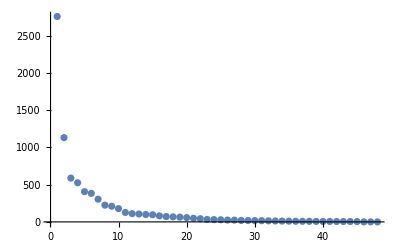

```mathematica
ListPlot[%333,PlotRange->All]
```